```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (EFT)

generic model {../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA_FC} initialized

classes model {../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA} initialized

in total: 2 Particles insertions

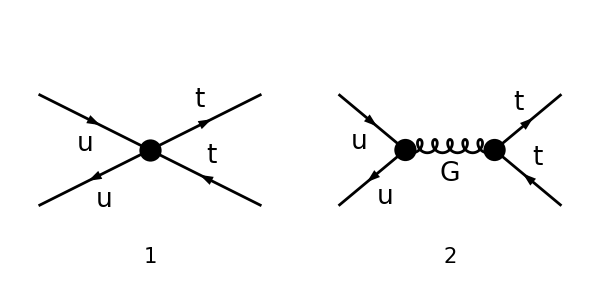

```mathematica
tops = CreateTopologies[0,2->2];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[tops,processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[2]}, GenericModel->"../../Models/Top-EFTphysical_simple-FA/Top-EFTphysical_simple-FA_FC"];
Paint[allDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT,GaugeXi[a__]->1},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},List->False,DropSumOver->True,LorentzIndexNames-> {μ,ν},SMP->True,List->False,Contract->False,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings];
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-ⅈ (1/(p1+p2)^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (4 A0 GS MT (φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-2 A0 GS ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1)))+GS.GS (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+B0 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(-k2)).γ^Ind25.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT)))

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampB)/.{GS.GS-> GS^2},Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]]
```

-(4 ⅈ A0 GS MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2-(4 ⅈ A0 GS MT T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2+(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2-(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))/(p1+p2)^2+(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2-(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT)))/(p1+p2)^2-3 ⅈ B0 δ_Col1Col3 δ_Col2Col4 (φ(-k2)).γ^Ind25.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))+ⅈ B0 δ_Col1Col2 δ_Col3Col4 (φ(-k2)).γ^Ind25.(φ(k1)) (φ(p1,MT)).γ^Ind25.(γ̄)^6.(φ(-p2,MT))+-(ⅈ GS^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2

```mathematica
ampEsimp=FullSimplify[ampE/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}]
```

-ⅈ ((φ(-k2)).γ^μ.(φ(k1)) ((GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (4 A0 MT ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))+GS (φ(p1,MT)).γ^μ.(φ(-p2,MT))))/(p1+p2)^2+B0 (3 δ_Col1Col3 δ_Col2Col4-δ_Col1Col2 δ_Col3Col4) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))-(2 A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))/(p1+p2)^2)

```mathematica
sps=Cases2[ampEsimp,Spinor]
moms=Cases2[ampEsimp,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^6,(γ̄)^7,γ^μ,γ·p1,γ·p2}

```mathematica
(* Simpligy A.GA[6].(1,GA[mu]).B + A.GA[7].B - > A.(1,GA[mu]).B  *)
simp1=Flatten[Table[sps[[a]].moms[[1]].sps[[b]]+sps[[a]].moms[[2]].sps[[b]]-> sps[[a]].sps[[b]],{a,1,Length[sps]},{b,1,Length[sps]}]];
simp2=Flatten[Table[sps[[a]].moms[[3]].moms[[1]].sps[[b]]+sps[[a]].moms[[3]].moms[[2]].sps[[b]]-> sps[[a]].moms[[3]].sps[[b]],{a,1,Length[sps]},{b,1,Length[sps]}]];
```

```mathematica
(* Peskin A.38: ∑_A Subscript[T, ij]^A Subscript[T, kl]^A = 1/2 (Subscript[δ, i,l] Subscript[δ, j,k] - 1/3 Subscript[δ, i,j] Subscript[δ, k,l]) *)
(* 6 ∑_A Subscript[T, c2c1]^A Subscript[T, c3c4]^A =  3 Subscript[δ, c2,c4] Subscript[δ, c1,c3] - Subscript[δ, c1,c2] Subscript[δ, c3,c4] *)
ampEsimp2=FullSimplify[ampEsimp/.Join[simp1,simp2]/.{(3*SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col3]]*SUNFDelta[SUNFIndex[Col2],SUNFIndex[Col4]]-SUNFDelta[SUNFIndex[Col1],SUNFIndex[Col2]]*SUNFDelta[SUNFIndex[Col3],SUNFIndex[Col4]])-> 6SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]]}]
```

-1/2 ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) (3 B0 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(2 GS (4 A0 MT+GS) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2)+(4 A0 GS (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p2).(φ(k1))-(φ(-k2)).(γ·p1).(φ(k1))))/(p1+p2)^2)

```mathematica
Collect[ampEsimp2,{sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]],sps[[2]].moms[[5]].sps[[1]]},Simplify]
```

-1/2 ⅈ T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(-k2)).γ^μ.(φ(k1)) (3 B0 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+(2 GS (4 A0 MT+GS) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))/(p1+p2)^2)+(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1)))/(p1+p2)^2-(2 ⅈ A0 GS T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1)))/(p1+p2)^2